#### Lattice depth and potential envelopes

As a function of distance along 111 the lattice depth is

```mathematica
vL111[ r_,s0_,w_]:=s0 Exp[- (4 r^2)/(3 w^2)]
```

This is also the envelope for the bottom of the potential

For the compensationg potential we have  the same equation

```mathematica
vC111[r_,g0_,w_]:=g0 Exp[- (4 r^2)/(3 w^2)]
```

The band zero is given by

```mathematica
Ezero[ r_, s0_,w_]:=3 √vL111[r,s0,w]
```

#### Full expression for the lowest band

```mathematica
band[r_,s0_,wL_,g0_,wC_]:= -3vL111[r,s0,wL] + 3 vC111[r,g0,wC] + Ezero[r,s0,wL]
```

#### Expansion of the potential around the center

```mathematica
Clear[r,s0,wL,g0,wC]
Series[ band[r,s0,wL,g0,wC],{r,0,4}]
```

3 (g0+√s0-s0)+(-(4 g0)/wC^2-(2 √s0)/wL^2+(4 s0)/wL^2) r^2+((8 g0)/(3 wC^4)+(2 √s0)/(3 wL^4)-(8 s0)/(3 wL^4)) r^4+O[r]^5

#### Compensation that gives quartic

```mathematica
Clear[r,s0,wL,g0,wC]
sol=Solve[ SeriesCoefficient[ band[r,s0,wL,g0,wC],{r,0,2}]==0,{g0}][[1]]
```

{g0→((-√s0+2 s0) wC^2)/(2 wL^2)}

#### Potential with the compensation that gives quartic, comparision between real deal and series expansion

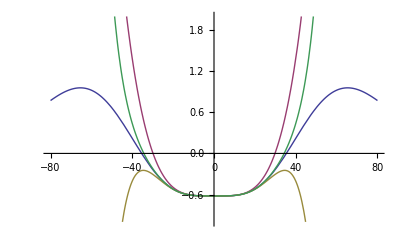

```mathematica
Clear[r,s0,wL,g0,wC]
series4  =Normal[Series[band[r,s0,wL,g0,wC],{r,0,4}]];
series6  =Normal[Series[band[r,s0,wL,g0,wC],{r,0,6}]];
series8  =Normal[Series[band[r,s0,wL,g0,wC],{r,0,8}]];
s0=7.;
wL=47.;
alpha=1.17;
wC =wL/alpha;
Plot[
{band[r,s0,wL,g0,wC]/.sol,
series4/.sol,
series6/.sol,
series8/.sol},
{r,-80,80},
PlotRange->{-1,2}]
```

The quartic expansion works well enough, so it can be used to analytically estimate the radius of the sample.

#### The coefficient for the r^4 term in the series expansion is obtained

```mathematica
Clear[r,s0,wL,g0,wC]
SeriesCoefficient[ band[r,s0,wL,g0,wC],{r,0,4}]/.sol/.{wC->wL/α^2}
```

(2 √s0)/(3 wL^4)-(8 s0)/(3 wL^4)+(4 (-√s0+2 s0) α^4)/(3 wL^4)

#### We solve the equation that defines half-filling, or also that makes this energy reach the threshold for evaporation. This equation gives is the fourth power of the half-filling radius.

```mathematica
-2(g0+√s0-s0)/.sol
```

-2 (√s0-s0+((-√s0+2 s0) wC^2)/(2 wL^2))

```mathematica
((2 √s0)/(3 wL^4)-(8 s0)/(3 wL^4)+(4 (-√s0+2 s0) α^4)/(3 wL^4))r4==
```

#### Radius that satisfies the half-filling condition

```mathematica
Solve[ A2 r2 + A4 r2^2 == U/2, {r2}]
```

{{r2→(-A2-√(A2^2+2 A4 U))/(2 A4)},{r2→(-A2+√(A2^2+2 A4 U))/(2 A4)}}

```mathematica
rHalf[g0_,s0_,wL_,wC_,U_]:=Module[{r},
r/.NSolve[(-(4 g0)/wC^2-(2 √s0)/wL^2+(4 s0)/wL^2) r^2+((8 g0)/(3 wC^4)+(2 √s0)/(3 wL^4)-(8 s0)/(3 wL^4)) r^4 == U/2,{r}][[4]]
]
```

```mathematica
s0=7.;
g0=(4 s0 -2 √s0)/(4 (wL/wC)^2);
wL=47.;
wC=47./1.18;
U=1.4;
r=rHalf[ g0,s0,wL, wC,U]
4/3 π (r/0.532)^3
```

30.5931

796571.

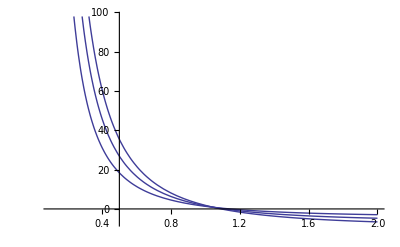

```mathematica
s0=7.;
Plot[Table[s0((1-α^2)/α^2) + √s0((2 α^2-1)/(2 α^2)),{s0,{7,10,13}}], {α,0.1, 2}]
```

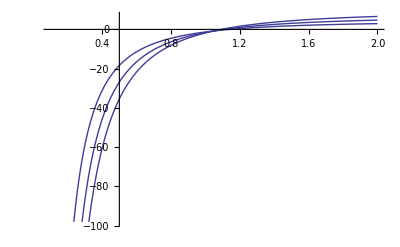

```mathematica
s0=7.;
Plot[Table[s0-√s0- (4 s0- 2 √s0)/(4 α^2),{s0,{7,10,13}}], {α,0.1, 2}]
```

```mathematica
Clear[s0,U];
sol=Solve[2(s0-√s0- (4 s0- 2 √s0)/(4 α2))-U/2==0,{α2}]
```

{{α2→(2 (-√s0+2 s0))/(-4 √s0+4 s0-U)}}

```mathematica
sol/.{s0->7.,U->2.}
```

{{α2→1.47295}}

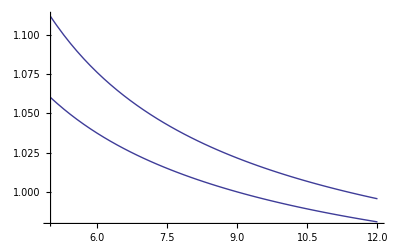

```mathematica
U=1.4;
Plot[Table[√(0.8(4 s0 - 2 √s0)/(4 s0-4 √s0-U)),{U,{0.,1.}}],{s0,5, 12}]
```